The Mathematica^® Journal

# Proyecto Álgebra Abstracta y Computacional 2023-2 On The Rapid Computation of Various Polylogarithmic Constants

Jaime Zamora Avilez
Juan Diego Murcia
Daniel Echeverri

Mathematica has many built-in functions for doing research in graph theory. Formerly it was necessary to load the Combinatorica package to access these functions; most are now available within Mathematica itself. This article studies a problem concerning the vertex coloring of graphs using Mathematica by introducing some user-defined functions.

## Unfriendly Colorings of Graphs

INTRODUCCION

A 2-coloring of a graph is unfriendly if each vertex lives in an unfriendly neighborhood, that is, at least half its neighbors are colored differently from itself. It is a theorem that every finite graph has an unfriendly coloring. (The situation is much more complicated for infinite graphs [1, 2]). The proof is clever, but not very long and we give it next. Define the mixing number of a colored graph to be the number of its edges whose vertices have different colors. Proceed by successively "flipping," that is, changing the color of those vertices that live in friendly neighborhoods. When a vertex is flipped, it may change the neighborhood status of other vertices; however, each flip increases the mixing number of the graph. Since the mixing number is bounded by the number of edges in the graph, this flipping process must eventually end with no more flippable vertices, that is, no more vertices living in friendly neighborhoods.

## Finding the Mixing Number of a Colored Graph

We start with an easy example. We first consider the complete graph with 7 vertices.

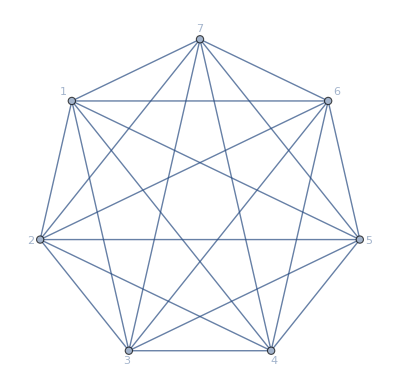

```mathematica
g7= CompleteGraph[7,VertexLabels->Automatic]
```

We will color the vertices either red or blue. Assume that we start with four blue and three red vertices.

```mathematica
blue7={1,2,3,4};
red7={5,6,7};
```

Here is how we show the colors.

```mathematica
graph[r_,b_][G_]:=Graph[G,VertexLabels->Automatic,VertexStyle->Flatten@{#->Blue&/@b,#->Red&/@r}]
```

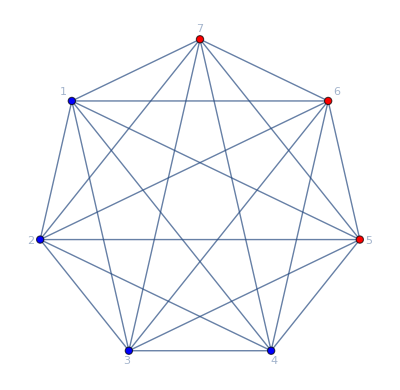

```mathematica
graph[red7,blue7][g7]
```

To calculate the mixing number, we first generate the set of edges.

```mathematica
E7=EdgeList@CompleteGraph@7
```

{1<->2,1<->3,1<->4,1<->5,1<->6,1<->7,2<->3,2<->4,2<->5,2<->6,2<->7,3<->4,3<->5,3<->6,3<->7,4<->5,4<->6,4<->7,5<->6,5<->7,6<->7}

Next we introduce MixedEdgeQ, which determines if the vertices of an edge have the different colors.

```mathematica
MixedEdgeQ[r_,b_][UndirectedEdge[x_,y_]]:=Or[
MemberQ[r,x]&&MemberQ[b,y],
MemberQ[b,x]&&MemberQ[r,y]
]
```

Then MixedEdges selects those edges whose vertices have different colors.

```mathematica
MixedEdges[r_,b_][e_]:=Select[e,MixedEdgeQ[r,b]]
```

Finally, we apply MixedEdges to E7.

```mathematica
MixedEdges[red7,blue7][E7]
```

{1<->5,1<->6,1<->7,2<->5,2<->6,2<->7,3<->5,3<->6,3<->7,4<->5,4<->6,4<->7}

This is the mixing number of E7.

```mathematica
Length[%]
```

12

It is easy to see by considering the other 2-colorings of g7 that this coloring has the maximum mixing number for the graph and hence this coloring must be unfriendly. Four of one color and three of the other gives a mixing number of 4×3, whereas five of one color and two of the other gives a mixing number of 5×2, and so on. Of course, a direct inspection also shows the coloring is unfriendly.

## A Larger Example

We used the RandomGraph function to construct a graph g20 with 20 vertices and 100 edges. Here is the list of edges that was generated.

```mathematica
E20={1<->2,1<->3,1<->4,1<->7,1<->9,1<->10,1<->12,1<->13,1<->14,1<->15,1<->16,1<->17,1<->19,1<->20,2<->8,2<->10,2<->11,2<->13,2<->15,2<->16,2<->17,2<->19,3<->4,3<->5,3<->6,3<->7,3<->8,3<->9,3<->18,3<->20,4<->5,4<->15,4<->17,4<->20,5<->7,5<->8,5<->11,5<->16,5<->19,5<->20,6<->7,6<->8,6<->9,6<->11,6<->13,6<->15,6<->16,6<->18,6<->19,6<->20,7<->8,7<->9,7<->12,7<->15,7<->17,7<->19,7<->20,8<->9,8<->12,8<->14,8<->15,8<->17,8<->19,9<->11,9<->12,9<->13,9<->15,9<->16,9<->17,9<->18,9<->19,10<->11,10<->12,10<->15,10<->16,10<->17,10<->19,11<->12,11<->14,11<->15,11<->16,11<->18,11<->19,12<->13,12<->14,12<->16,12<->17,12<->18,13<->14,13<->15,13<->16,13<->19,14<->15,14<->19,15<->16,15<->20,16<->18,16<->19,16<->20,17<->19};
```

Arbitrarily color the first 10 vertices red and the remaining 10 blue.

```mathematica
red20=Range[10];
blue20=Range[11,20];
```

Here is the image of the graph, colored as before.

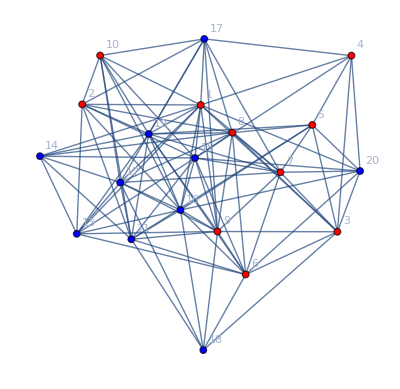

```mathematica
graph[red20,blue20][E20]
```

The function flip changes the color of a vertex.

```mathematica
flip[r_,b_][v_]:=If[
MemberQ[r,v],
{DeleteCases[r,v],Append[b,v]},
{Append[r,v],DeleteCases[b,v]}
]
```

For example, this flips vertex 1.

```mathematica
flip[red20,blue20][1]
```

{{2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20,1}}

We need to get the set of neighbors of a vertex v in a graph G, that is, those vertices that share an edge with v. Since the built-in Mathematica function NeighborhoodGraph[G,v] includes the vertex v itself, we remove it.

```mathematica
neighbors[G_,v_]:= DeleteCases[VertexList@NeighborhoodGraph[G,v],v]
```

For example, here are the neighbors of vertex 3 in g20.

```mathematica
neighbors[Graph[E20],3]
```

{1,4,7,9,20,8,5,6,18}

Next we obtain the edges whose vertices are colored differently.

```mathematica
MixedEdges[red20,blue20][E20]
```

{1<->12,1<->13,1<->14,1<->15,1<->16,1<->17,1<->19,1<->20,2<->11,2<->13,2<->15,2<->16,2<->17,2<->19,3<->18,3<->20,4<->15,4<->17,4<->20,5<->11,5<->16,5<->19,5<->20,6<->11,6<->13,6<->15,6<->16,6<->18,6<->19,6<->20,7<->12,7<->15,7<->17,7<->19,7<->20,8<->12,8<->14,8<->15,8<->17,8<->19,9<->11,9<->12,9<->13,9<->15,9<->16,9<->17,9<->18,9<->19,10<->11,10<->12,10<->15,10<->16,10<->17,10<->19}

The length of that list is the mixing number of the graph with edges E20 and the color partition {red20,blue20}.

```mathematica
Length[%]
```

54

Call a vertex v a secure vertex in a graph G if v lives in a friendly neighborhood, that is, v has the same color as most of its neighbors in G.

The function SecureVertexQ determines whether v is a secure vertex in G with the color partition {r,b}.

```mathematica
SecureVertexQ[r_,b_][G_,v_]:=
Or[
MemberQ[r,v]&&Length[neighbors[G,v]∩r] >Length[neighbors[G,v]∩b],MemberQ[b,v]&&Length[neighbors[G,v]∩b]>Length[neighbors[G,v]∩r]
]
```

For example, these are the secure vertices of g20.

```mathematica
sv=Select[Range@20,SecureVertexQ[red20,blue20][E20,#]&]
```

{3,7,8,11,12,13,14,16}

We define the corresponding function, SecureVertices.

```mathematica
SecureVertices[r_,b_][G_]:=Select[VertexList[G],SecureVertexQ[r,b][G,#]&]
```

## One Step of Unfriendly Coloring a Graph

We select the first element v in the list of secure vertices sv and set the colors.

```mathematica
v =First@sv
```

3

```mathematica
r=red20;
b=blue20;
```

We flip the color of v since it lives in a friendly neighborhood, or equivalently, it is a secure vertex.

```mathematica
flip[r,b][3]
```

{{1,2,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20,3}}

We could now repeat this step using the generated color partition and stop when there are no more secure vertices. In the next section we write the function UnfriendlyColor to carry out the process to the end, with output the final color partition.

## Unfriendly Coloring a Graph

The following short program produces an unfriendly coloring of any 2-colored graph starting with the color partition {red,blue}.

```mathematica
UnfriendlyColor[red_,blue_][G_]:=Module[
{r,b,sv,v},
{r,b}={red,blue};
sv=SecureVertices[r,b][G];
While[
sv≠{},
v=First@sv;
{r,b}=flip[r,b][v];
sv=SecureVertices[r,b][G];
];
{r,b}
]
```

Here is the unfriendly color partition.

```mathematica
uc20=UnfriendlyColor[red20,blue20][E20]
```

{{1,2,4,5,6,9,10,12,14,7},{11,13,15,16,17,18,19,20,3,8}}

Here is the unfriendly coloring of the graph g20.

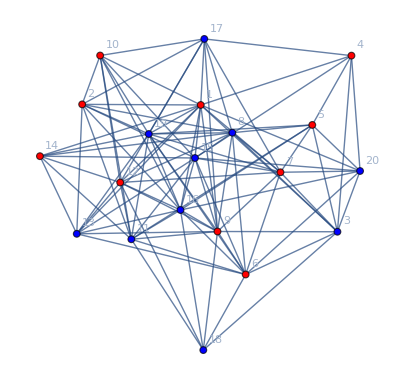

```mathematica
Apply[graph,uc20][E20]
```

We can even start with all vertices having the same color, say red.

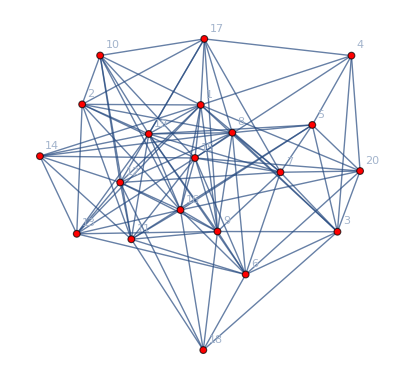

```mathematica
graph[Range@20,{}][E20]
```

We run our program and use the new color partition.

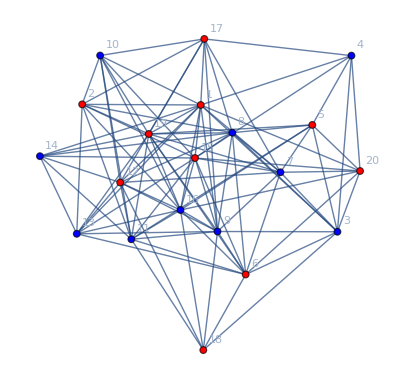

```mathematica
Apply[graph,UnfriendlyColor[Range@20,{}][E20]][E20]
```

## Relation to the Max-Cut Problem

The max-cut problem is to partition the vertices V of a graph G into two sets S and V\S so as to maximize the number of edges whose endpoints are in both sets. However, this is equivalent to a two-coloring of the vertices of G such that the size of the max cut (i.e. the number of edges joining the two cut sets) is the same as the mixing number of the coloring. The max-cut problem is known to be NP-hard [3, 4], which implies that methods of finding this maximum will not run in polynomial time unless P = NP, something most mathematicians consider unlikely.

In the context of the max-cut problem, our procedure, UnfriendlyColor, is known as local search and can easily be shown to always produce a cut with at least half the number of edges in the graph [3].

## Conclusion

We have shown how to find unfriendly 2-colorings of finite graphs, which can easily be extended to more colors. We feel that treating a vertex coloring as a partition of the list of vertices and regarding this as an integral and dynamic part of the graph should be of use in investigating other coloring problems.

Finally, I wish to dedicate this work to Bill Emerson, who worked on this problem with me over 30 years ago (see reference 3 in [1] to our unpublished paper). Bill was a very talented mathematician and a good friend. He is missed by all who knew him.

## Acknowledgements

I am grateful to George Beck for improving my programming throughout the paper and to Professor Lenore Cowen for pointing out the connection to the max-cut problem.

## References

R. Aharoni, E. C. Milner and K. Prikry, “Unfriendly Partitions of a Graph,” Journal of Combinatorial Theory, Series B, 50(1), 1990 pp. 1–10. https://doi.org/10.1016/0095-8956(90)90092-E.

S. Shelah and E. C. Milner, “Graphs with No Unfriendly Partitions,” A Tribute to Paul Erdős (A. Baker, B. Bollobás and A. Hajnal, eds.), Cambridge, UK: Cambridge University Press, 1990 pp. 373–384.

D. Panigrahi, “COMPSCI 638: Graph Algorithms, Lecture 22.” (Sep 10, 2021) https://courses.cs.duke.edu//fall19/compsci638/fall19_notes/lecture22.pdf.

M. R. Garey, D. S. Johnson and L. Stockmeyer, “Some Simplified NP-Complete Problems,” in Proceedings of the Sixth Annual ACM Symposium on Theory of Computing, New York: ACM, Seattle, WA, 1974 pp. 47–63. https://dl.acm.org/doi/10.1145/800119.803884.

R. Cowen, “Mixing Numbers and Unfriendly Colorings of Graphs,” The Mathematica Journal, 2021. doi.org/10.3888/tmj.23–4.

About the Author

Robert Cowen is a Professor Emeritus at Queens College, CUNY. His main research interests are logic and combinatorics. He has enjoyed teaching students how to use Mathematica to do research in mathematics for many years.

Robert Cowen
16422 75th Avenue
Fresh Meadows, NY 11366
robert.cowen@gmail.com